```mathematica
g=9.8(*grav. constant*)
(*vter = Sqrt[m g/c]*)
V = 50
th = 40*Pi/180
sol = With[{vter=50}, NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]), {y[0] == 2, x[0] ==0}, {y'[0] == V Sin[th],x'[0] ==V Cos[th]}}, {x,y}, {t,0,200}]]
```

9.8

50

(2 π)/9

{{x→InterpolatingFunction[{{0.,200.}},<>],y→InterpolatingFunction[{{0.,200.}},<>]}}

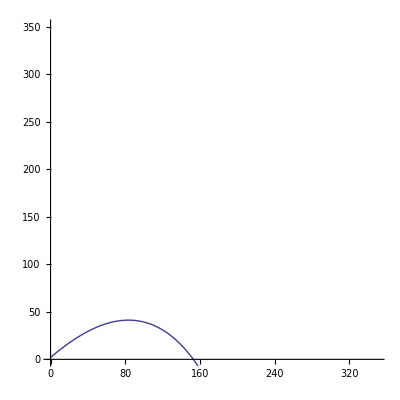

```mathematica
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,200}, PlotRange-> {0,350}]
```

```mathematica
Manipulate[
Module[
{sol = NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]), {y[0] == 2, x[0] ==0}, {y'[0] == V Sin[th],x'[0] ==V Cos[th]}}, {x,y}, {t,0,200}]},
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tf}, PlotRange-> {0,350}]],
{{V, 20, "Initial Velocity (m/s)"}, 20,100, Appearance -> "Labeled"},
{{vter,30,"Terminal Velocity (m/s)"},30,100,Appearance->"Labeled"},{{th,.1,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,0.01,"time elapsed (s)"},0.01,18.,Appearance->"Labeled"}]
```

```mathematica
Manipulate[
Module[
{sol = NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]), {y[0] == 2, x[0] ==0}, {y'[0] == V Sin[th],x'[0] ==V Cos[th]}}, {x,y}, {t,0,200}]},
ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tf}, PlotRange-> {0,350}]],
{{V, 20, "Initial Velocity (m/s)"}, 20,100, Appearance -> "Labeled"},
{{vter,30,"Terminal Velocity (m/s)"},30,100,Appearance->"Labeled"},{{th,.1,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,0.01,"time elapsed (s)"},0.01,18.,Appearance->"Labeled"}]
```

NDSolve::ndnum: Encountered non-numerical value for a derivative at t == 0..

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 2.04082×10^-7 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 2.04082×10^-7 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[
 is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::dsvar: 0.000204286 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

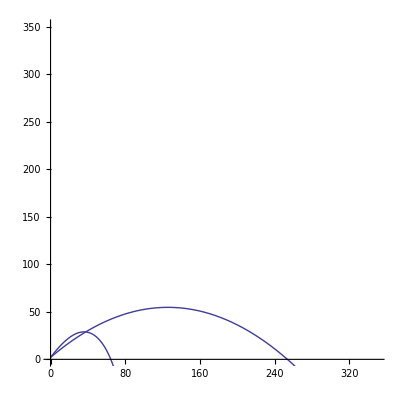

```mathematica
Manipulate[
Module[
{sol = NDSolve[{x''[t]==(-g x'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2],y''[t] ==-g (1+(y'[t]/vter^2) Sqrt[x'[t]^2+y'[t]^2]), {y[0] == 2, x[0] ==0}, {y'[0] == V Sin[th],x'[0] ==V Cos[th]}}, {x,y}, {t,0,200}]},{Z[t_] := V Cos[th] t ,
Y[t_] := 2+V Sin[th] t-.5 g t^2}
{plotty=ParametricPlot[Evaluate[{x[t],y[t]}/.sol],{t,0,tf}, PlotRange-> {0,350}],
MYPLOT = ParametricPlot[Evaluate[{Z[t],Y[t]}], {t,0,tf}, PlotRange-> {0,350}]}],
{{V, 20, "Initial Velocity (m/s)"}, 20,100, Appearance -> "Labeled"},
{{vter,30,"Terminal Velocity (m/s)"},30,100,Appearance->"Labeled"},{{th,.1,"initial angle (rad)"},.1,π/2,Appearance->"Labeled"},
{{tf,0.01,"time elapsed (s)"},0.01,18.,Appearance->"Labeled"}]
Show[{MYPLOT,plotty}]
```